ImportanceSampling_common.m loaded.

ImportanceSampling_decagonal.m loaded.

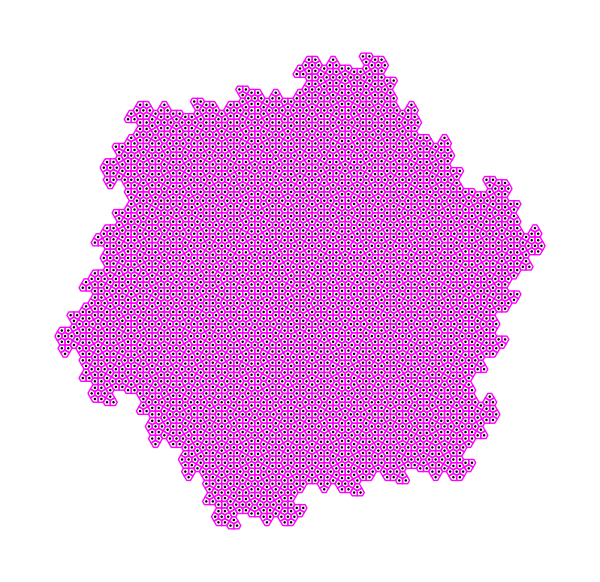

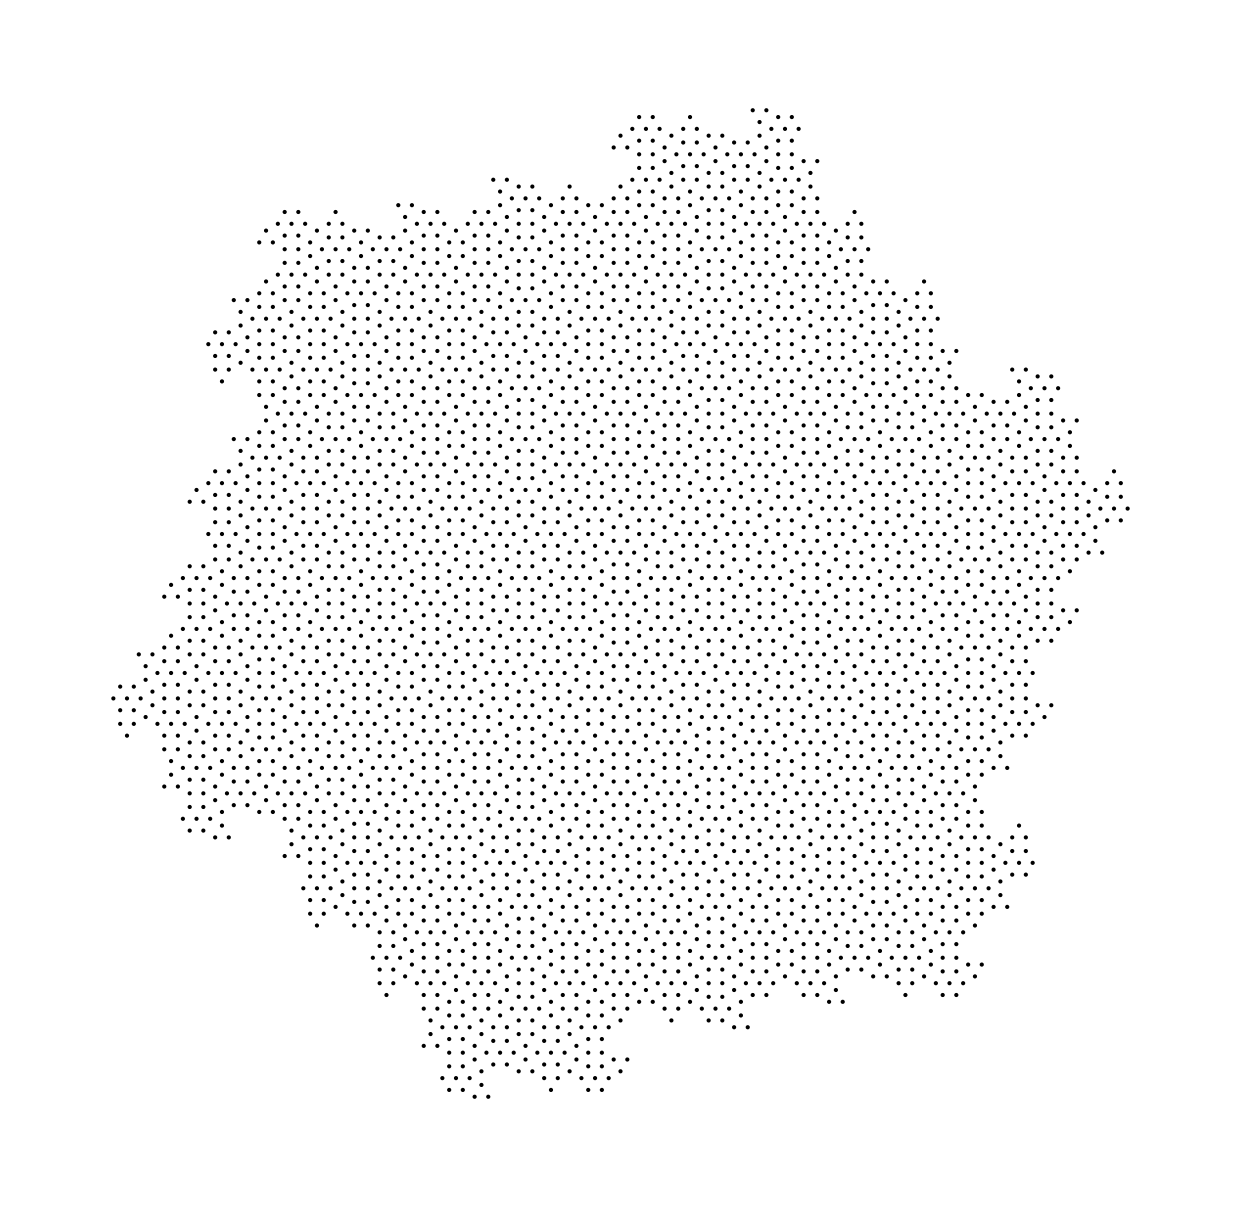

```mathematica
(************
    dodecagonal_half_vertBased_showInflations.nb
  V.O.UdeM january 2004
  october 2005 - version with 1d_lds

seedmx={ (* dodecagonal-half, variant 2-3-7  *)
          (* 1 2 3 4 5 6 7 8 910 1 2 3 4 5 *)
      (*1*) {0,0,0,1,0,1,1,0,0,0},
      (*2*) {0,0,0,0,0,0,0,5,1,1},
      (*3*) {1,1,0,0,0,0,0,0,0,0},
      (*4*) {0,0,0,0,0,0,0,4,2,1},
      (*5*) {1,1,0,0,0,0,0,0,0,0},
      (*6*) {0,0,0,1,1,1,0,0,0,0},
      (*7*) {0,0,0,1,0,1,1,0,0,0},
      (*8*) {0,0,0,1,1,1,0,0,0,0},
      (*9*) {0,1,1,0,0,0,0,0,0,0},
      (*10*){0,0,0,0,0,0,0,0,6,1}
            };
	eigenval: 2 + Sqrt[3] = 3.73205080756887729352744634151
	eigenvec: {(3 + 5*Sqrt[3])/18, (13 + 5*Sqrt[3])/18, (1 + 2*Sqrt[3])/9, (7 + 2*Sqrt[3])/9, (1 + 2*Sqrt[3])/9, (2*(1 + Sqrt[3]))/9, (3 + 5*Sqrt[3])/18, (2*(1 + Sqrt[3]))/9, (1 + Sqrt[3])/6, 1}
			   {0.647792,            1.20335,             0.496011,            1.16268,             0.496011,       0.607122,             0.647792,             0.607122,           0.455342,   1.}
*******)

lbl="dodecagonal_half_vertBased_TYPE237";

workingDirectory="c:\\Documents and Settings\\ostrom\\My Documents\\prep_dodecagonal\\dodeca_half_TYPE237";\

SetDirectory[workingDirectory];
Get["ImportanceSampling_common.m"];
Get["ImportanceSampling_dodecagonal_half_vertBased.m"];

SetOptions[Graphics,ImageSize\[Rule]{950,Automatic}];
SetOptions[Graphics,ImageSize\[Rule]{1200,Automatic}];
SetOptions[Graphics,ImageSize\[Rule]{600,Automatic}];
font="Courier";textsz=12;
(*-----------------------------params-----------------------------*)
rng=All;
niter=6;

showTileType=False;
showTileType=True;

showFcode = False;
cutOutOfRangeFlag=False;
shapeTrianlesOnly=False;
shapecol=Blue;
{edgecol1,edgecol2,edgecol3,edgecol4}={Cyan,RGBColor[.9,.7,0],Red,Green};

showdir=False;

fillFigure=False;
showEdges=False;
showAmmannBars=False;
(*-----------------------------end of params-----------------------------*)

(*------------------------------------prog starts here------------------------------------*)

{px,py}={1.6,-1.6};
n=3;
shapesgl=gl={};
Do[maxLOS=iter;
    plbl=ToString[lbl]<>" iter="<>ToString[iter]<>" "<>date;
    gl={};
    type=10;
      {x,y}={0,0};
      fig=getFigure[type,{x,y},0,1,{i}];
      shapecol=getColor[iter];
      flst=recursiveSubdiv[fig];
(******************
      AppendTo[gl,getGLst[flst]];
    p=Show[Graphics[{PointSize[.003],shapesgl}],
        AspectRatio\[Rule]Automatic,
        PlotRange\[Rule]rng];
	Print[p];
**********************)
    (*epsOut["p_"<>lbl<>"_iter"<>ToString[iter]<>".eps",p];*)
    ,{iter,0,niter}];
pts = #[[2]] & /@ flst;
shapesgl=gl={};
shapecol = Magenta;
getGLst[flst];
p=Show[Graphics[{PointSize[.003],Point/@pts,shapesgl}],
        AspectRatio\[Rule]Automatic,
        PlotRange\[Rule]rng];
Print[p];
Graphics[Point /@ pts]//Print;
(*------------------------------------prog ends here------------------------------------*)
```